```mathematica
SetDirectory[NotebookDirectory[]];
```

# h_scaling

## data

```mathematica
fpi=Flatten[Import["./LPAp_mub0/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub0/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub0/buffer/c.dat"]]*197.33^3;
datamub0=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub0=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub0linear=Transpose[{h[[2;;Length[h]-2]],Flatten[Table[FindFit[datamub0[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPAp_mub300/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub300/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub300/buffer/c.dat"]]*197.33^3;
datamub300=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub300=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub300linear=Transpose[{h[[2;;Length[h]-2]],Flatten[Table[FindFit[datamub300[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
fpi=Flatten[Import["./LPAp_mub400/buffer/fpi.dat"]];
Zphi=Flatten[Import["./LPAp_mub400/buffer/Zphi.dat"]];
h=Flatten[Import["./LPAp_mub400/buffer/c.dat"]]*197.33^3;
datamub400=Transpose[{Log[h[[2;;Length[h]]]],Log[fpi[[2;;Length[h]]]/√Zphi[[2;;Length[h]]]]}];
h1mub400=Transpose[{Log[h[[2;;Length[h]-2]]],1/Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
h1mub400linear=Transpose[{h[[2;;Length[h]-2]],Flatten[Table[FindFit[datamub400[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[h]-2}]]}];
```

## Plot

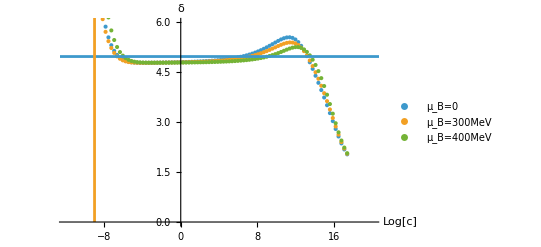

```mathematica
ploth=Show[ListPlot[{h1mub0,h1mub300,h1mub400},AxesLabel->{"Log[c]","δ"},PlotLegends->{"μ_B=0","μ_B=300MeV","μ_B=400MeV","μ_B=500MeV"(*,"μ_B=600MeV","μ_B=650MeV","μ_B=700MeV"*)},Axes->True,PlotRange->{{-12,20},{0,6}}],ListLinePlot[{{{-20,4.975},{100,4.975}},{{Log[0.05^3],0},{Log[0.05^3],100}}}]]
```

```mathematica
(*Export["hscaling.pdf",ploth]*)
```

```mathematica
(*Export["mub0data.dat",h1mub0]*)
```